```mathematica
rcar=ResourceFunction["RandomCellularAutomatonRule"];
```

```mathematica
StripZeros=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list]},
If[
(* AllZeros *)
Module[{i0=Length[list]}, While[i0>0&&list[[i0]]==0, i0--;]; i0==0],
 Return[Table[0, {iter, 0}]]
];
While[list[[i]]==0, i++];
 While[list[[j]]==0, j--]; 
list[[i;;j]]
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
```

```mathematica
FindRepeatDeterministicIndexByStripZerosCompiled=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 2]],
With[{StripZeros=Function[Typed[list2, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list2]},
While[list2[[i]]==0&&i<j, i++];
 If[i<j,While[list2[[j]]==0, j--]]; 
If[i==j,Table[0, 0],list2[[i;;j]]]]
]},
Module[{i=Length[list]-1, last=StripZeros[list[[-1]]]},
 While[i>0&&StripZeros[list[[i]]]!=last, i--]; If[i==0, 0,i+1]
]]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3}];

FindRepeatDeterministicByStripZeros[list_List]:=StripZeros/@list[[FindRepeatDeterministicIndexByStripZerosCompiled[list];;]]
```

```mathematica
AvgTimeToPeriodicity[rule_Integer, r_Integer]:=Module[{res},
res=Table[CellularAutomaton[{rule, 2, r}, {RandomInteger[1, 100], 0}, 100], 30];
Median[(FindRepeatDeterministicIndexByStripZerosCompiled/@res)/.(0->100)]
]
```

```mathematica
CAClass3Or4[rule_Integer, r_Integer]:=Module[{n=100, res, res2},
res=Table[CellularAutomaton[{rule, 2, r}, {RandomInteger[1, 100], 0}, {{{100}}}], n];
If[Total[Unitize[Total/@res]]<0.2n||(Median[Length/@res]<=120&&Median[Total/@res]<40&&AvgTimeToPeriodicity[rule, r]>=30), 4, 3]
]

CAClassSingle[rule_Integer, r_Integer]:=Module[{res, bcall, bclast,frdlen},
res=CellularAutomaton[{rule, 2, r}, RandomInteger[1, 100], 100];
bcall=ByteCount[Compress[res]];
bclast=ByteCount[Compress[Last[res]]];
frdlen=FindRepeatDeterministicIndexByStripZerosCompiled[res]/.(0->100);
Which[Length[Union[Last[res]]]==1, 1, bclast<100 || bcall<1000||frdlen<=20, 2, True, CAClass3Or4[rule, r]]
]

CAClass[rule_Integer, r_Integer]:=First[Commonest[Table[CAClassSingle[rule, r], 10]]]
```

```mathematica
SortBy[ParallelSelect[ParallelTable[rcar[{2, 2}, "Quiescent"->True,"Type"->"Symmetric"][["RuleNumber"]], 1000],CAClass[#, 2]>=4&], AvgTimeToPeriodicity[#, 2]&]
```

{3663504292,1132372520,1332674120,1565568184,1789712212,2400996904,2862371684,3096581360,1962209188,3412767832,7632756,376192720,731791912,985421552,1005347464,1076007252,1444862964,1447886528,1481946848,1755500884,2029430448,2217761888,2250787092,2270964264,2417251056,2474533544,2620673712,2783211032,2847150712,3169073872,3327983476,3330210660,3373432888,3395221364,3445947992,3771785508,3902985556,190456888,3245778488,3325991536,3818833464}

```mathematica
Column[Labeled[ArrayPlot[CellularAutomaton[{#, 2, 2}, {RandomInteger[1, 500], 0}, 100], ImageSize->Full], ClickToCopy[#]]&/@]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
roi={1841737240,1266460216,635846232,2038859416,2605475480}
```

{1841737240,1266460216,635846232,2038859416,2605475480}

```mathematica
Column[Labeled[ArrayPlot[CellularAutomaton[{#, 2, 2}, {RandomInteger[1, 1000], 0}, 300], ImageSize->Full], ClickToCopy[#]]&/@roi]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

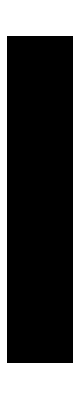
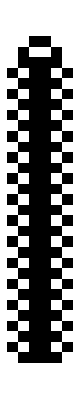
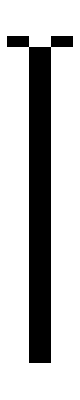
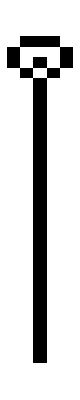
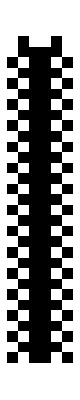
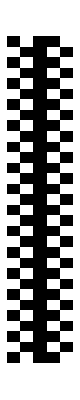
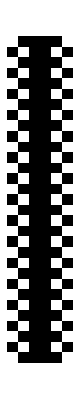
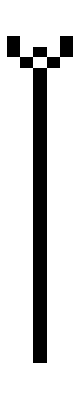
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-1841737240
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-1266460216
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-635846232
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-2038859416
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-2605475480

```mathematica
Column[Labeled[Row[Table[ArrayPlot[CellularAutomaton[{#, 2, 2}, {IntegerDigits[i, 2], 0}, 30]], {i, Select[Range[1, 100, 2], #<=IntegerReverse[#, 2]&]}]],ClickToCopy[#]]&/@roi]
```

```mathematica
2038859416
```

2038859416

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#, 2, 2}, {RandomInteger[1, 300], 0}, 100], ImageSize->Full], ClickToCopy[#]]&@635846232
```

-Graphics-

```mathematica
<<(ParentDirectory[NotebookDirectory[]]<>"/DetectPeriodTools.wl")
```

```mathematica
VisualizeDetectPeriod[{2038859416, 2, 2}, RandomInteger[2^100], None, ImageSize->Medium]
```

-Graphics--Graphics-

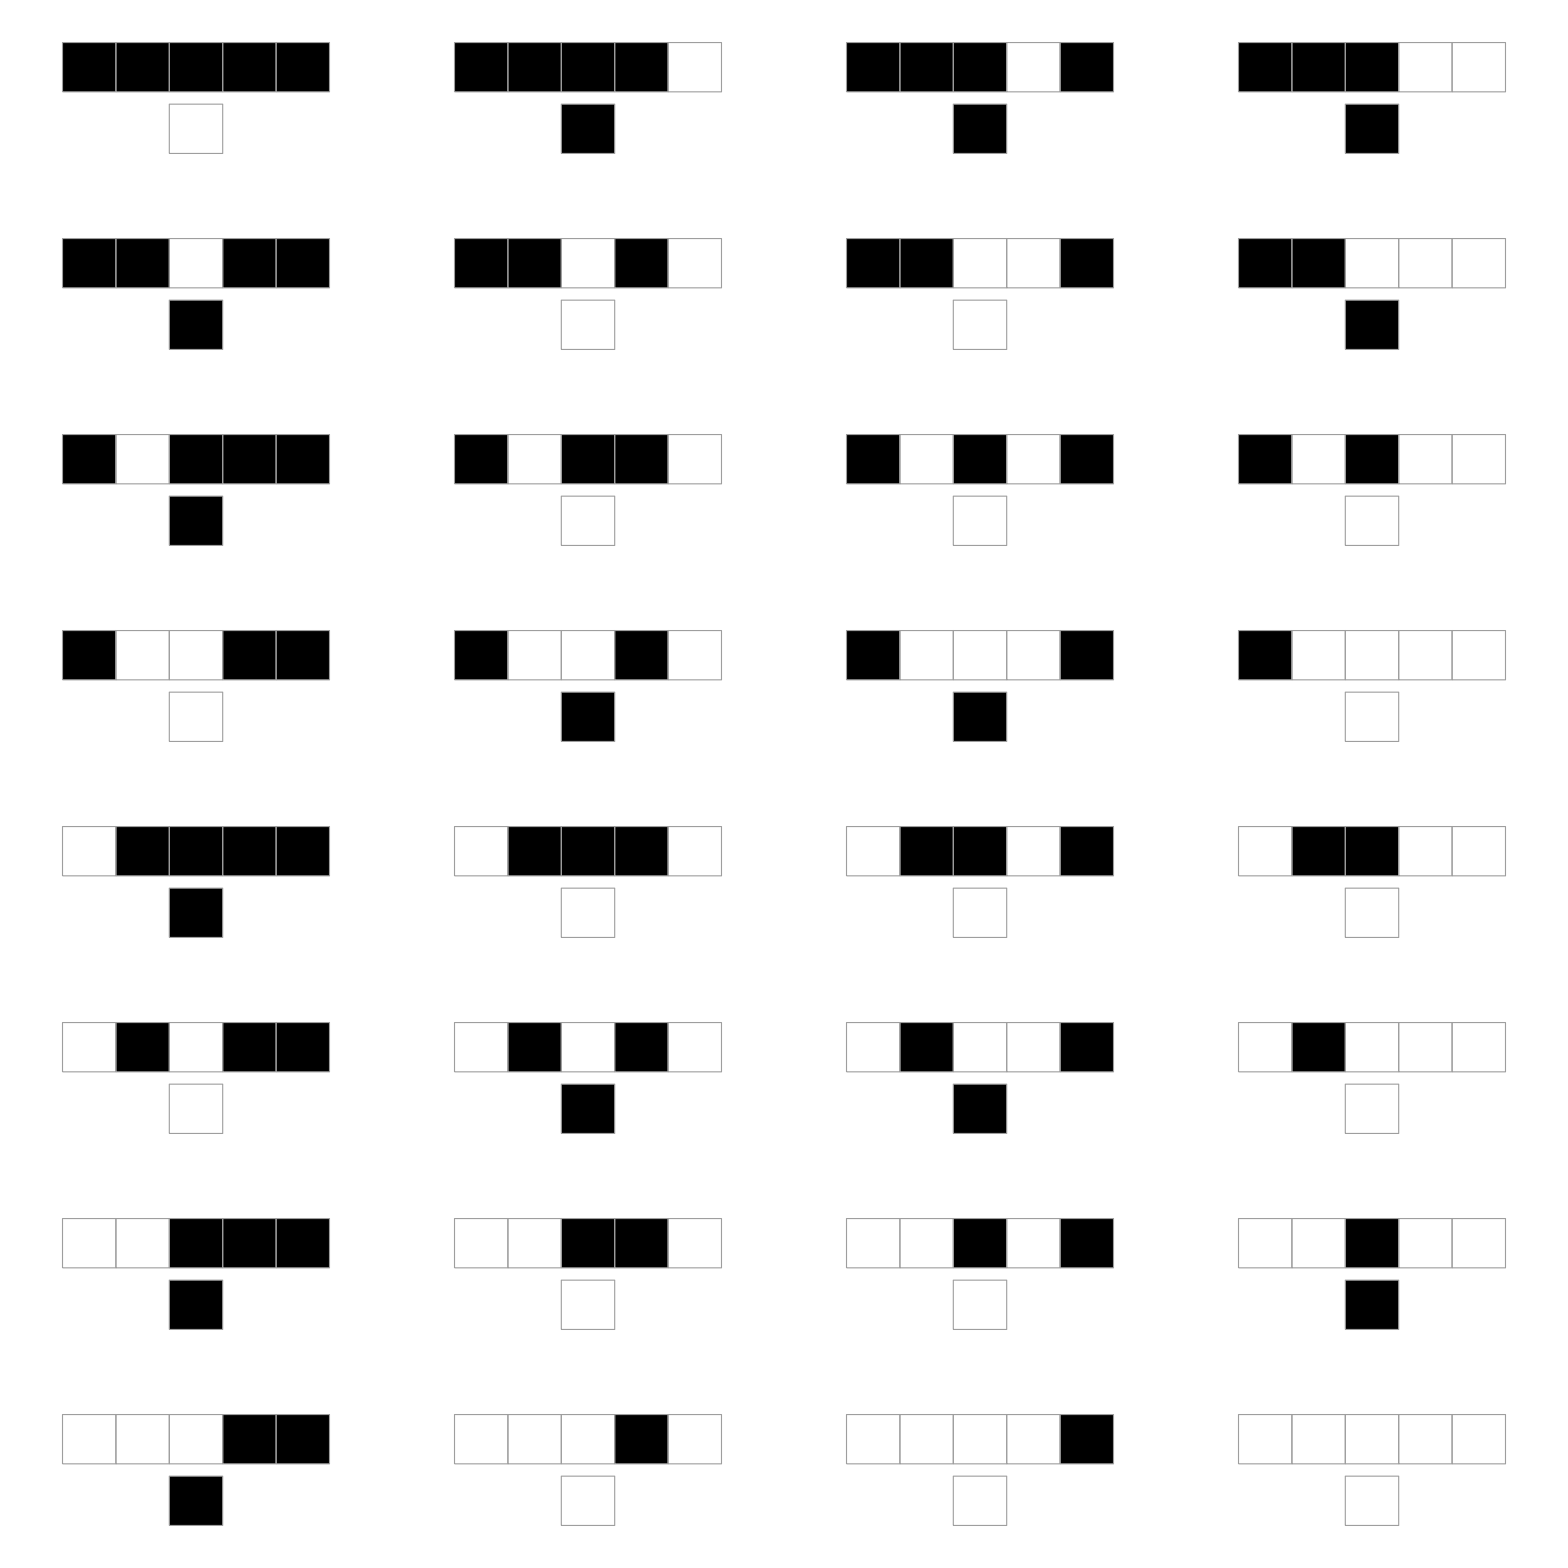

```mathematica
RulePlot[CellularAutomaton[{2038859416, 2, 2}]]
```

```mathematica
BooleanConvert[BooleanFunction[2038859416, 5], "BDT"]
```

(#1&&!((#2&&((#3&&#4&&#5)||(!#3&&!((#4&&#5)||(!#4&&!#5)))))||(!#2&&!((#3&&#4&&#5)||(!#3&&!((#4&&#5)||(!#4&&!#5)))))))||(!#1&&((#2&&((#3&&#4&&#5)||(!#3&&!((#4&&#5)||(!#4&&!#5)))))||(!#2&&((#3&&((#4&&#5)||(!#4&&!#5)))||(!#3&&#4&&#5)))))&

```mathematica
SortBy[{"DNF","CNF", "ESOP", "ANF", "NOR", "NAND", "NOR2", "NAND2", "AND", "OR", "IMPLIES", "IF","BDT"}, LeafCount[BooleanConvert[BooleanFunction[2038859416, 5], #]]&]
```

{ANF,IF,BDT,DNF,NAND,IMPLIES,ESOP,OR,CNF,NOR,AND,NAND2,NOR2}

```mathematica
BooleanConvert[BooleanFunction[2038859416, 5], "ANF"][a, b, c, d, e]
```

c⊻(a&&b)⊻(a&&c)⊻(a&&d)⊻(a&&e)⊻(b&&c)⊻(b&&d)⊻(b&&e)⊻(c&&d)⊻(c&&e)⊻(d&&e)⊻(a&&b&&c)⊻(a&&b&&d)⊻(a&&b&&e)⊻(a&&d&&e)⊻(b&&d&&e)⊻(c&&d&&e)⊻(a&&b&&d&&e)

```mathematica
BooleanConvert[%21/.{a->#1,b->#2, c->#3, d->#4, e->#5}, "BFF"]
```

BooleanFunction[…][#1,#2,#3,#4,#5]

```mathematica
BooleanConvert[((c⊻(a||b))&&(c⊻(d||e)))⊻(a&&b)⊻(d&&e)/.{a->#1,b->#2, c->#3, d->#4, e->#5}, "BFF"]
```

BooleanFunction[…][#1,#2,#4,#5,#3]

```mathematica
Boole[((c⊻(a||b))&&(c⊻(d||e)))⊻(a&&b)⊻(d&&e)/.{a->#1,b->#2, c->#3, d->#4, e->#5}&@@@Positive[Tuples[{0, 1}, 5]]]//FromDigits[Reverse[#], 2]&
```

2038859416

```mathematica
2038859416
```

```mathematica
StringReplace[ToString[StandardForm[((c⊻(a||b))&&(c⊻(d||e)))⊻(a&&b)⊻(d&&e)
]], {"⊻"->"^", "&&"->"&", "||"->"|"}]
```

(a&b)^(d&e)^((c^(a|b))&(c^(d|e)))

```mathematica
res=Developer`ToPackedArray[Last[ReadList["/home/chris/Programming/GPU/opencl2/out.txt"], 0]];
Length[res]
UnitConvert[Quantity[N@ByteCount[res], "Bytes"], "Kilobytes"]
```

265

2.408 kB

```mathematica
res2=DedupSame[Join@@ParallelMap[DetectPeriod[{2038859416, 2, 2}, #]&, res]][[All, "Original"]];
Length[res2]
```

9

```mathematica
Labeled[AArrayPlot[{2038859416, 2, 2}, #, 300], ClickToCopy[#]]&/@Rest[Sort[res2]][[;;UpTo[30]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
StringReplace[ToString[StandardForm[First@MinimalBy[BooleanConvert[BooleanFunction[635846232, 5][a, b, c, d, e], #]&/@{"DNF","CNF", "ESOP", "ANF", "NOR", "NAND", "NOR2", "NAND2", "AND", "OR", "IMPLIES", "IF","BDT"}, LeafCount]]]
, {"⊻"->"^", "&&"->"&", "||"->"|"}]
```

c^(a&b)^(a&c)^(a&d)^(a&e)^(b&d)^(b&e)^(c&e)^(d&e)^(a&b&c)^(a&b&e)^(a&c&e)^(a&d&e)^(c&d&e)

```mathematica
res=Developer`ToPackedArray[Last[ReadList["/home/chris/Programming/GPU/opencl2/out.txt"], 0]];
Length[res]
UnitConvert[Quantity[N@ByteCount[res], "Bytes"], "Kilobytes"]
```

53

0.552 kB

```mathematica
Labeled[AArrayPlot[{635846232, 2, 2}, #, 300], ClickToCopy[#]]&/@Rest[Sort[res]][[;;UpTo[60]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
StringReplace[ToString[StandardForm[First@MinimalBy[BooleanConvert[BooleanFunction[2783211032, 5][a, b, c, d, e], #]&/@{"DNF","CNF", "ESOP", "ANF", "NOR", "NAND", "NOR2", "NAND2", "AND", "OR", "IMPLIES", "BDT"}, LeafCount]]]
, {"⊻"->"^", "&&"->"&", "||"->"|", "!"->"~"}]
```

(a&b&~c&~e)|(a&~b&d&~e)|(a&c&e)|(~a&b&~c&d)|(~a&b&d&~e)|(~a&b&~d&e)|(~a&~b&c&~d&~e)|(~a&~c&d&e)

```mathematica
res=Developer`ToPackedArray[Last[ReadList["/home/chris/Programming/GPU/opencl2/out.txt"], 0]];
Length[res]
UnitConvert[Quantity[N@ByteCount[res], "Bytes"], "Kilobytes"]
```

273

2.408 kB

```mathematica
res2=DedupSame[Join@@ParallelMap[DetectPeriod[{2783211032, 2, 2}, #]&, res]][[All, "Original"]];
Length[res2]
```

231

```mathematica
Labeled[AArrayPlot[{2783211032, 2, 2}, #, 300], ClickToCopy[#]]&/@RandomSample[res, 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
|
```

## new

```mathematica
CAClass//Definition
```

CAClass[rule_Integer,r_Integer]:=First[Commonest[Table[CAClassSingle[rule,r],10]]]

```mathematica
CAClass[2404331018,2]
```

3